```mathematica
a=Exp[-x];
b=(-2+Exp[-x](2+2x+x^2))/x^3;
```

```mathematica
a + 3b//FullSimplify
```

(ⅇ^-x (6-6 ⅇ^x+x (6+x (3+x))))/x^3

```mathematica
Series[a+3b,{x,0,6}]
```

-x/4+x^2/5-x^3/12+x^4/42-x^5/192+x^6/1080+O[x]^7

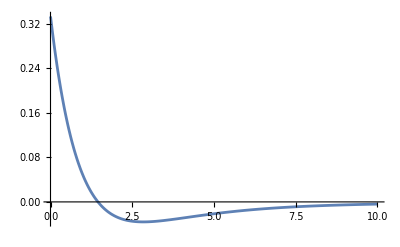

```mathematica
Plot[a+2b,{x,0.001,10},PlotRange->All]
```

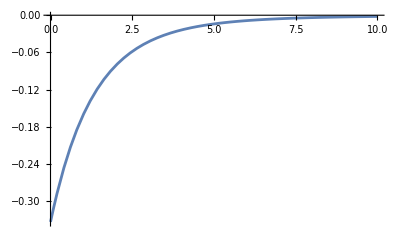

```mathematica
Plot[b,{x,0.001,10},PlotRange->All]
```